# Volume computations for 3D moving sofa problem baselines

This notebook contains code to compute the volume of two baselines for the 3D moving sofa problem, described in Problem 6.5 of Mathematical Discovery and Exploration at Scale by Georgiev, Gómez-Serrano, Tao and Wagner, 2025.
Specifically, it computes:
1. The intersection between the Gerver sofa lying in the xy plane (x being the long side) extruded to 0 <= z <= 1, and the Gerver sofa lying in the xz plane (x being the long side) extruded to 0 <= y <= 1.
2. The intersection between the Gerver sofa lying in the xy plane (x being the long side) extruded to 0 <= z <= 1, and the unit diameter cylinder (x,y,z): (y-0.5)^2 + (z-0.5)^2 <= 0.25.
We find (1) to be approximately 1.74 and (2) to be approximately 1.77.

To define the 2D Gerver sofa shape, we use the following code from Appendix 3 of Solving Moving Sofa Problem Using Calculus of Variations by Zhipeng Deng, https://arxiv.org/pdf/2407.02587.

```mathematica
α1p=0.078;
α2p=1.78;
t0=0.7103;
ri=0.61;
pts=2001;
αα=Range[0.,π/2,(π/2-0.)/(pts-1)];
dfdα=NDSolve`FiniteDifferenceDerivative[{1},{αα},"DifferenceOrder"->4]["DifferentiationMatrix"];
d2fdα2=NDSolve`FiniteDifferenceDerivative[{2},{αα},"DifferenceOrder"->4]["DifferentiationMatrix"];

Do[
nL=Length[αα];
varsr=Table[Unique[r$],{nL}];
varst=Table[Unique[t$],{nL}];
(*discrete ODE1-piecewise EL equation*)
eqns1=(-Cos[αα/2]-2 (-3 Cos[αα]+Cos[2 αα]) varsr+Sin[αα/2]+2 (-3 Cos[αα]+Cos[2 αα]) varst+12 Sin[αα] dfdα.varsr-3 Sin[2 αα] dfdα.varsr-6 Sin[αα] dfdα.varst+3 Sin[2 αα] dfdα.varst+d2fdα2.varsr-6 Cos[αα] d2fdα2.varsr+Cos[2 αα] d2fdα2.varsr+d2fdα2.varst-Cos[2 αα] d2fdα2.varst)*(Boole[0<=#<α1p]&/@αα)+(-Cos[αα/2]-2 (-3 Cos[αα]+Cos[2 αα]) varsr+Sin[αα/2]+2 (-2 Cos[αα]+Cos[2 αα]) varst+12 Sin[αα] dfdα.varsr-3 Sin[2 αα] dfdα.varsr-4 Sin[αα] dfdα.varst+3 Sin[2 αα] dfdα.varst+d2fdα2.varsr-6 Cos[αα] d2fdα2.varsr+Cos[2 αα] d2fdα2.varsr+d2fdα2.varst-Cos[2 αα] d2fdα2.varst)*(Boole[α1p<=#<π-α2p]&/@αα)+(-Cos[αα/2]+4 Cos[αα] varsr+Sin[αα/2]-2 Cos[αα] varst+8 Sin[αα] dfdα.varsr-2 Sin[αα] dfdα.varst-4 Cos[αα] d2fdα2.varsr)*(Boole[π-α2p<=#<=π/2]&/@αα);
(*discrete ODE2-piecewise EL equation*)
eqns2=(Cos[αα/2]+Sin[αα/2]+2 varsr (3 Sin[αα]+Sin[2 αα])-2 (3 Sin[αα]+Sin[2 αα]) varst+dfdα.varsr-6 Cos[αα] dfdα.varsr-3 Cos[2 αα] dfdα.varsr+dfdα.varst+12 Cos[αα] dfdα.varst+3 Cos[2 αα] dfdα.varst-Sin[2 αα] d2fdα2.varsr+6 Sin[αα] d2fdα2.varst+Sin[2 αα] d2fdα2.varst)*(Boole[0<=#<α1p]&/@αα)+ (Cos[αα/2]+Sin[αα/2]+4 (1+Cos[αα]) varsr Sin[αα]-2 (3 Sin[αα]+Sin[2 αα]) varst+dfdα.varsr-4 Cos[αα] dfdα.varsr-3 Cos[2 αα] dfdα.varsr+dfdα.varst+12 Cos[αα] dfdα.varst+3 Cos[2 αα] dfdα.varst-Sin[2 αα] d2fdα2.varsr+6 Sin[αα] d2fdα2.varst+Sin[2 αα] d2fdα2.varst)*(Boole[α1p<=#<π-α2p]&/@αα)+(Cos[αα/2]+Sin[αα/2]+2 varsr Sin[αα]-4 Sin[αα] varst-2 Cos[αα] dfdα.varsr+8 Cos[αα] dfdα.varst+4 Sin[αα] d2fdα2.varst)*(Boole[π-α2p<=#<=π/2]&/@αα);
(*boundary conditions
-1/2+2 r[0]-2 t[0]-2 r''[0]=0
r'[π/2]=0
t[0]=t0
t'[π/2]=0*)
eqns1[[1]]=(-1/2+2varsr[[1]]-2varst[[1]]-2(d2fdα2.varsr)[[1]])-0;
eqns1[[nL]]=(dfdα.varsr)[[nL]]-0;
eqns2[[1]]=varst[[1]]-t0;
eqns2[[nL]]=(dfdα.varst)[[nL]]-0;
(*all equatoins and variables*)
govEq=Join[eqns1,eqns2];
allVars=Join[varsr,varst];
(*solve discretized ODEs*)root=FindRoot[govEq,Thread[{allVars,Flatten[{Table[ri,nL],Table[t0,nL]}]}],MaxIterations->50,AccuracyGoal->Infinity,PrecisionGoal->8];
sol=allVars/.root;
(*interpolation to obtain r[α] and t[α]*)
{rsoltemp,tsoltemp}=Partition[sol,nL];
rsol=Interpolation[Transpose[{αα,rsoltemp}]];
tsol=Interpolation[Transpose[{αα,tsoltemp}]];
(*obtain curves*)
AA={rsol[α]*Cos[α],tsol[α]*Sin[α]};
AAp={rsol[α]*Cos[α]+√2*Cos[π/4+α/2],tsol[α]*Sin[α]+√2*Sin[π/4+α/2]};
BB={rsol[α]*Cos[α]-tsol[α]*2 Cos[α/2]^2,0};
BBp={rsol[α]*Cos[α]-tsol[α]*2 Cos[α/2]^2-1/Sin[α/2],0};
CC={rsol[α]*Cos[α]+tsol[α]*Sin[α]*Tan[α/2],0};
CCp={rsol[α]*Cos[α]+tsol[α]*Sin[α]*Tan[α/2]+1/Cos[α/2],0};
EAABBx=1/2* (-1+2 Cos[α]+Cos[2 α]) rsol[α]-2 Cos[α/2]^2 Cos[α] tsol[α]+Sin[α] (Cos[α] rsol'[α]-(1+Cos[α]) tsol'[α]);
EAABBy=-2 Sin[α/2]^2 (rsol[α] Sin[α]-Sin[α] tsol[α]-Cos[α] rsol'[α]+tsol'[α]+Cos[α] tsol'[α]);
EAACCx=rsol[α] (Cos[α]+Sin[α]^2)-2 Cos[α] Sin[α/2]^2 tsol[α]+Sin[α] (-Cos[α] rsol'[α]+(-1+Cos[α]) tsol'[α]);
EAACCy=2 Cos[α/2]^2 (-rsol[α] Sin[α]+Sin[α] tsol[α]+Cos[α] rsol'[α]+tsol'[α]-Cos[α] tsol'[α]);
EAApBBpx=1/2* ((-1+2 Cos[α]+Cos[2 α]) rsol[α]-2 Sin[α/2]-4 Cos[α/2]^2 Cos[α] tsol[α]+Sin[2 α] rsol'[α]-2 Sin[α] tsol'[α]-Sin[2 α] tsol'[α]);
EAApBBpy=1/2* (2 Cos[α/2]+rsol[α] (-2 Sin[α]+Sin[2 α])-2 (-1+Cos[α]) Sin[α] tsol[α]-rsol'[α]+2 Cos[α] rsol'[α]-Cos[2 α] rsol'[α]-tsol'[α]+Cos[2 α] tsol'[α]);
EAApCCpx=1/2* (2 Cos[α/2]+2 rsol[α] (Cos[α]+Sin[α]^2)+(1-2 Cos[α]+Cos[2 α]) tsol[α]-Sin[2 α] rsol'[α]-2 Sin[α] tsol'[α]+Sin[2 α] tsol'[α]);
EAApCCpy=1/2* (2 Sin[α/2]-2 (1+Cos[α]) rsol[α] Sin[α]+(2 Sin[α]+Sin[2 α]) tsol[α]+rsol'[α]+2 Cos[α] rsol'[α]+Cos[2 α] rsol'[α]+tsol'[α]-Cos[2 α] tsol'[α]);
(*find α1p α2p*)
ααres=FindRoot[{rsol[αα1]*Cos[αα1]==-EAABBx/.α->(π-αα2),tsol[αα1]*Sin[αα1]==EAABBy/.α->(π-αα2)},{αα1,0.1},{αα2,1.8}];
(*print iteration difference of α1p α2p*)
α1p=ααres[[1]][[2]];
α2p=ααres[[2]][[2]];
,{5}(*iterate for 5 times*)]//Quiet;
```

Calculate the exact area of the 2D Gerver sofa.

```mathematica
exactArea = -2 rsol[0]+4 tsol[0]+2*NIntegrate[-EAApBBpy*D[EAApBBpx,α]-EAApCCpy*D[EAApCCpx,α],{α,0,π/2},WorkingPrecision->500,MaxRecursion->30,AccuracyGoal->8]+2*NIntegrate[tsol[α]*Sin[α]*D[rsol[α]*Cos[α],α],{α,α1p,π/2},WorkingPrecision->500,MaxRecursion->30,AccuracyGoal->8]-2*NIntegrate[EAABBy*D[EAABBx,α],{α,0,π-α2p},WorkingPrecision->500,MaxRecursion->30,AccuracyGoal->8]
Print["exactArea: ", exactArea];
```

2.21953

exactArea: 2.21953

The following code defines the 2D Gerver sofa region by joining together the 12 line segments into a filled shape.

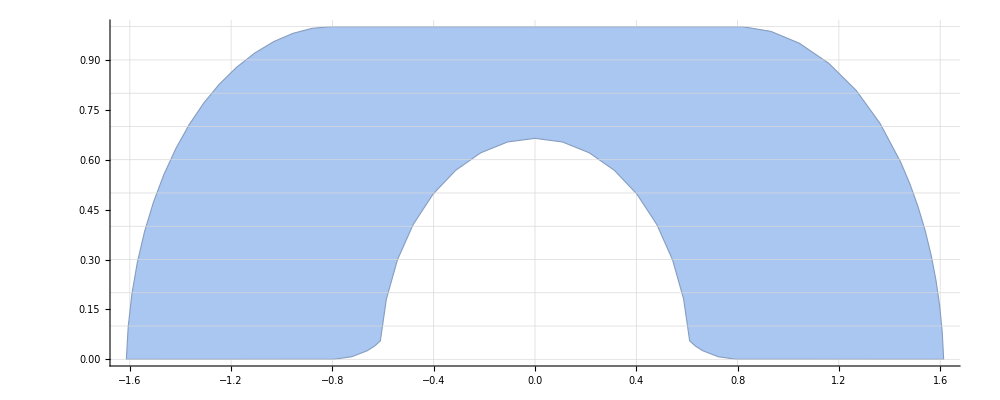

```mathematica
(* Define step size resolution for curve segments *)
alphaStep = 0.0001;  (* A smaller value gives a more precise shape *)

(* Curve 1: outer lower right *)
curvedEdge1=BSplineCurve[Table[{EAApCCpx,EAApCCpy},{α,0,Pi/2,alphaStep}]];

(* Curve 2: outer upper right *)
curvedEdge2=BSplineCurve[Table[{-EAApBBpx,EAApBBpy},{α,Pi/2,0,-alphaStep}]];

(* Straight edge 3: outer upper right *)
startPoint3={-EAABBx/.α->0,1};
endPoint3={0,1};
straightEdge3=Line[{startPoint3,endPoint3}];

(* Straight edge 4: outer upper left *)
startPoint4={0,1};
endPoint4={EAABBx/.α->0,1};
straightEdge4=Line[{startPoint4,endPoint4}];

(* Curve 5: outer upper left *)
curvedEdge5=BSplineCurve[Table[{EAApBBpx,EAApBBpy},{α,0,π/2,alphaStep}]];

(* Curve 6: outer lower left *)
curvedEdge6=BSplineCurve[Table[{-EAApCCpx,EAApCCpy},{α,π/2,0,-alphaStep}]];

(* Straight edge 7: lower left *)
startPoint7={x,0}/.x->(-EAApCCpx/.α->0);
endPoint7={x,0}/.x->(EAABBx/.α->0);
straightEdge7=Line[{startPoint7,endPoint7}];

(* Curve 8: inner lower left *)
curvedEdge8=BSplineCurve[Table[{EAABBx,EAABBy},{α,0,π-α2p, alphaStep}]];

(* Curve 9: inner middle lower left *)
curvedEdge9=BSplineCurve[Table[{-AA[[1]], AA[[2]]},{α,α1p,π/2, alphaStep}]];

(* Curve 10: inner middle lower right *)
curvedEdge10=BSplineCurve[Table[{AA[[1]], AA[[2]]},{α,π/2,α1p,-alphaStep}]];

(* Curve 11: inner lower right *)
curvedEdge11=BSplineCurve[Table[{-EAABBx,EAABBy},{α,π-α2p,0, -alphaStep}]];

(* Straight edge 12: lower right *)
startPoint12={x,0}/.x->(-EAABBx/.α->0);
endPoint12={x,0}/.x->(EAApCCpx/.α->0);
straightEdge12=Line[{startPoint12,endPoint12}];

(* Define region *)
mySofa = Graphics[{EdgeForm[{Thick,Black}],LightYellow,FilledCurve[{curvedEdge1,curvedEdge2,straightEdge3, straightEdge4, curvedEdge5, curvedEdge6, straightEdge7, curvedEdge8, curvedEdge9, curvedEdge10, curvedEdge11, straightEdge12}]},Axes->True];
sofaRegion=DiscretizeGraphics[mySofa];

(* Show the region *)
Show[sofaRegion,Axes->True, GridLines -> {Range[-2,2,0.1], Range[0, 1, 0.1]}, ImageSize-> 1000, Method->{"GridLinesInFront"->True}]

(* Define membership function *)
isInsideGerverSofa[{x_?NumericQ,y_?NumericQ}]:=RegionMember[sofaRegion,{x,y}]
```

```mathematica
(* Test membership function *)
isInsideGerverSofa[{1,0.3}]
isInsideGerverSofa[{0.5,0.3}]
```

True

False

## Volume calculation 1

We now compute the volume of the intersection between the Gerver sofa lying in the xy plane (x being the long side) extruded to 0 <= z <= 1, and the Gerver sofa lying in the xz plane (x being the long side) extruded to 0 <= y <= 1.
This is equal to the integral of sofaHeight(x)^2 over x, where sofaHeight(x) is the height of the 2D Gerver sofa at x.
We estimate this integral over a grid of x values.

```mathematica
(* Grid Parameters *)
step = 0.001;  (* Reduce this to get a more precise estimate *)
xmin=-1.7;
xmax=1.7;
ymin=0;
ymax=1;

(* Estimate sofaHeight for all x *)
heightData=Table[{x,Sum[Boole[isInsideGerverSofa[{x,y}]]*step,{y,ymin + (step/2),ymax - (step/2),step}]},{x,xmin + (step/2),xmax- (step/2),step}];

(* Calculate and print result *)
estimatedArea = Sum[step*(item[[2]]),{item,heightData}];  (* Estimated area of the 2D Gerver sofa, for accuracy comparison *)
estimatedVolume=Sum[step*(item[[2]])^2,{item,heightData}]; (* Estimated volume of the XY Gerver sofa intersected with the XZ Gerver sofa *)
Print["Step size: ", step];
Print["Estimated Area of 2D Gerver sofa for comparison: ", estimatedArea, " (Diff from Exact Area: ", Abs[estimatedArea - exactArea], ")"];
Print["Estimated Volume of extruded XY Gerver sofa intersected with extruded XZ Gerver sofa: ",estimatedVolume];
```

Step size: 0.001

Estimated Area of 2D Gerver sofa for comparison: 2.22001 (Diff from Exact Area: 0.000478373)

Estimated Volume of extruded XY Gerver sofa intersected with extruded XZ Gerver sofa: 1.73911

# Volume calculation 2

We now compute the volume of the intersection between the Gerver sofa lying in the xy plane (x being the long side) extruded to 0 <= z <= 1, and the unit diameter cylinder (x,y,z): (y-0.5)^2 + (z-0.5)^2 <= 0.25.
This is equal to the integral of the function 2 * sqrt(0.25 - (y-0.5)^2), over all (x,y) in the 2D Gerver sofa.
We estimate this integral over a grid of (x,y) points.

```mathematica
(* Define the function to integrate *)
f[y_]:=2*Sqrt[0.25-(y-0.5)^2]

(* Grid Parameters *)
step = 0.001;  (* Reduce this to get a more precise estimate *)
xmin=-1.7;
xmax=1.7;
ymin=0;
ymax=1;

(* Compute volume *)
totalPoints=0;  (* Number of points tested *)
insideCount=0;  (* Number of tested points that are inside the sofa *)
sumOfValues=0;  (* Sum of f(x,y) for (x,y) in the sofa *)
Do[Do[totalPoints++; If[isInsideGerverSofa[{x,y}],sumOfValues+=f[y]; insideCount++;],{x,xmin + (step/2),xmax-(step/2),step}],{y,ymin+ (step/2),ymax-(step/2),step}];

(* Calculate and Print Result *)
estimatedArea=insideCount* step* step;  (* Estimated area of the 2D Gerver sofa, for accuracy comparison *)
estimatedVolume=sumOfValues*step*step;  (* Estimated volume of the extruded Gerver sofa intersected with the cylinder *)
Print["Step size: ", step];
Print["Estimated Area of 2D Gerver sofa for comparison: ", estimatedArea, " (Diff from Exact Area: ", Abs[estimatedArea - exactArea], ")"];
Print["Estimated Volume of extruded Gerver sofa intersected with cylinder: ",estimatedVolume];
```

Step size: 0.001

Estimated Area of 2D Gerver sofa for comparison: 2.22001 (Diff from Exact Area: 0.000478373)

Estimated Volume of extruded Gerver sofa intersected with cylinder: 1.76988